```mathematica
pdfordk[x_,n_,k_]:=n Binomial[n-1,k-1](1-x)^((n-1)-(k-1))x^(k-1);
```

```mathematica
Refine[∫_0^x pdfordk[y,n,k]ⅆy,n>0&&k>0&&x≤1]
```

n Beta[x,k,1-k+n] Binomial[-1+n,-1+k]

```mathematica
cdfordk[x_,n_,k_]:=n  Binomial[n-1,k-1]Beta[x,k,n-k+1];
```

```mathematica
delta[x_,n_,dnk_:1]:=∑_(k=n-dnk)^(n-1) cdfordk[x,n,k]-cdfordk[x,n,n];
```

```mathematica
Solve[D[delta[x,n,1],x]==0,x]
```

{{x→(-1+n)/n}}

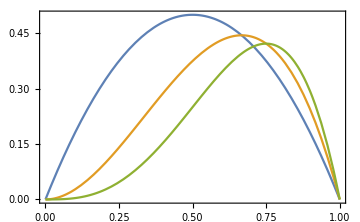

```mathematica
Plot[{delta[x,2],delta[x,3],delta[x,4]},{x,0,1},ImageSize->Medium,PlotRange->All,Frame->True]
```

```mathematica
draws=RandomReal[{0,1},{100000,1000}];
```

```mathematica
maxs=Map[Max,draws];
```

General::munfl: 0.0000204286^1000. is too small to represent as a normalized machine number; precision may be lost.

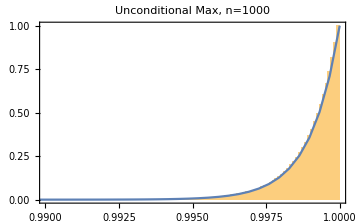

```mathematica
Show[Histogram[maxs,{10^-4},"CDF",PlotRange->{{0.990,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional Max, n=1000"],
Plot[cdfordk[x,1000,1000],{x,0,1},ImageSize->Medium,PlotRange->{{0.990,1},All},Frame->True,PlotLabel->"Unconditional Max, n=1000"]]
```

```mathematica
fmax2[list_]:=Max[Complement[list,{Max[list]}]];
```

```mathematica
max2s=Map[fmax2,draws];
```

General::munfl: Exp[-10794.7] is too small to represent as a normalized machine number; precision may be lost.

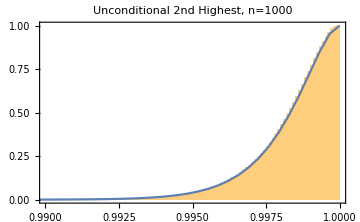

```mathematica
Show[Histogram[max2s,{10^-4},"CDF",PlotRange->{{0.990,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional 2nd Highest, n=1000"],
Plot[cdfordk[x,1000,1000-1],{x,0,1},ImageSize->Medium,PlotRange->{{0.990,1},All},Frame->True,PlotLabel->"Unconditional 2nd Highest, n=1000"]]
```

```mathematica
maxs990=Map[Max[Take[#,-10]]&,draws];
```

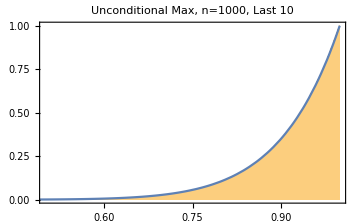

```mathematica
Show[Histogram[maxs990,{10^-3},"CDF",PlotRange->{{0.50,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional Max, n=1000, Last 10"],
Plot[cdfordk[x,10,10],{x,0,1},ImageSize->Medium,PlotRange->{{0.50,1},All},Frame->True,PlotLabel->"Unconditional Max, n=1000, Last 10"]]
```

```mathematica
max2s990=Map[fmax2[Take[#,-10]]&,draws];
```

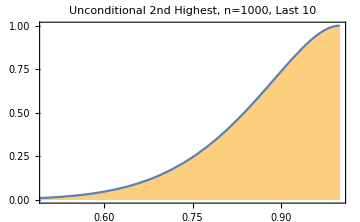

```mathematica
Show[Histogram[max2s990,{10^-3},"CDF",PlotRange->{{0.50,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional 2nd Highest, n=1000, Last 10"],
Plot[cdfordk[x,10,10-1],{x,0,1},ImageSize->Medium,PlotRange->{{0.50,1},All},Frame->True,PlotLabel->"Unconditional 2nd Highest, n=1000, Last 10"]]
```

```mathematica
maxs990cond=Map[If[Max[Take[#,-10]]==Max[#],{Max[#]},{}]&,draws];
```

```mathematica
Take[maxs990cond,50]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{0.998092},{},{},{},{},{},{},{},{},{},{},{},{},{},{0.999652},{},{},{},{},{},{},{},{},{}}

```mathematica
Flatten[Take[maxs990cond,50]]
```

{0.998092,0.999652}

General::munfl: 0.0000204286^1000. is too small to represent as a normalized machine number; precision may be lost.

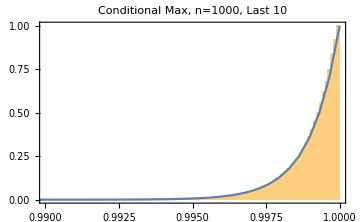

```mathematica
Show[Histogram[Flatten[maxs990cond],{10^-4},"CDF",PlotRange->{{0.990,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional Max, n=1000, Last 10"],
Plot[cdfordk[x,1000,1000],{x,0,1},ImageSize->Medium,PlotRange->{{0.990,1},All},Frame->True,PlotLabel->"Conditional Max, n=1000, Last 10"]]
```

```mathematica
max2s990cond=Map[If[Max[Take[#,-10]]==Max[#],{fmax2[#]},{}]&,draws];
```

General::munfl: Exp[-10794.7] is too small to represent as a normalized machine number; precision may be lost.

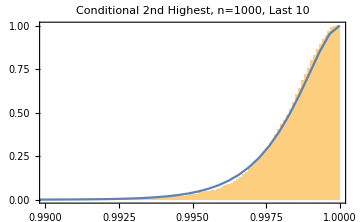

```mathematica
Show[Histogram[Flatten[max2s990cond],{10^-4},"CDF",PlotRange->{{0.990,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional 2nd Highest, n=1000, Last 10"],
Plot[cdfordk[x,1000,1000-1],{x,0,1},ImageSize->Medium,PlotRange->{{0.990,1},All},Frame->True,PlotLabel->"Conditional 2nd Highest, n=1000, Last 10"]]
```